```mathematica
GenerateTransitionProbabilities[currentSpace_]:=Module[{transitionProbability,space},
space = currentSpace;
Table[
Which[
index== Mod[space+1,40],
transitionProbability=1/36,
index== Mod[space+2,40],
transitionProbability=1/18,
index== Mod[space+3,40],
transitionProbability=1/12,
index== Mod[space+4,40],
transitionProbability=1/9,
index== Mod[space+5,40],
transitionProbability=5/36,
index== Mod[space+6,40],
transitionProbability=1/6,
index== Mod[space+7,40],
transitionProbability=5/36,
index== Mod[space+8,40],
transitionProbability=1/9,
index== Mod[space+9,40],
transitionProbability=1/12,
index== Mod[space+10,40],
transitionProbability=1/18,
index== Mod[space+11,40],
transitionProbability=1/36,
True,
transitionProbability=0
]
,{index,0,39}]
]

Chance[currentSpace_]:=Module[{space},
space=currentSpace;
Do[
If[
(i==8||i==23||i==37),
(*Nearest Utility*)
Which[
i==8,
space[[13]]+=space[[i]]*(1/16),
i==23,
space[[29]]+=space[[i]]*(1/16),
i==37,
space[[13]]+=space[[i]]*(1/16)
];
space[[25]]+=space[[i]]*(1/16);
space[[1]]+=space[[i]]*(1/16);
(*Nearest Railroad*)
Which[
i==8,
space[[16]]+=space[[i]]*(1/16),
i==23,
space[[26]]+=space[[i]]*(1/16),
i==37,
space[[6]]+=space[[i]]*(1/16)
];
space[[11]]+=space[[i]]*(1/16);
space[[6]]+=space[[i]]*(1/16);
space[[40]]+=space[[i]]*(1/16);
space[[i-3]]+=space[[i]]*(1/16);
space[[12]]+=space[[i]]*(1/16);
space[[i]]*=7/16;,
Null
]
,{i,1,40}
];
space
];

CommunityChest[currentSpace_]:=Module[{space},
space=currentSpace;
Do[
If[
(i==3||i==18||i==34),
space[[1]]+=space[[i]]*(1/16);
space[[11]]+=space[[i]]*(1/16);
space[[i]]*=14/16;,
Null
]
,{i,1,40}
];
space
];

GenerateMonopolyBoard:=Module[{board},
board=Table[
CommunityChest[Chance[GenerateTransitionProbabilities[i]]]
,{i,1,40}];
Return[board]
]
```

```mathematica
myBoard=GenerateMonopolyBoard;
Manipulate[ListLinePlot[myBoard[[x]]],{x,1,40,1}]
```

```mathematica
init = PadRight[{1},40]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

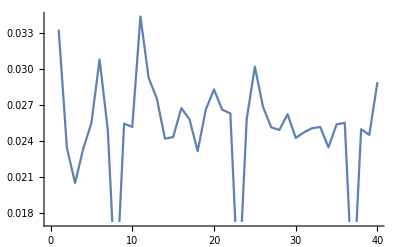

```mathematica
a=N@NestList[#.myBoard&,init,100][[100]];
ListLinePlot[a]
```